```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/shi/file/git/baryon_number_fluc/mub500data/v2

```mathematica
data=Import["./Shi_T-mu_500.0-flag_4-21x120_VC=true_abstol1e-3.csv"];
```

```mathematica
data[[1]]
```

{T_mu,σ,ω₀,n_B,P,ϵ}

```mathematica
data[[2]][[1]]
```

(0.0, 460.1118481127528)

```mathematica
Head[data[[2]][[1]]]
```

String

```mathematica
StringCases[data[[2]][[1]],NumberString]
```

{0.0,460.1118481127528}

```mathematica
T=ToExpression[Table[StringCases[data[[i]][[1]],NumberString][[1]],{i,2,121}]];
mub=ToExpression[Table[StringCases[data[[i*120+2]][[1]],NumberString][[2]],{i,0,20}]];
p=Table[Table[data[[j*120+i]][[5]],{i,2,121}],{j,0,20}];
```

```mathematica
plotdata=Table[Transpose[{T[[2;;120]],p[[i]][[2;;120]]*197.33^3}],{i,1,21}];
```

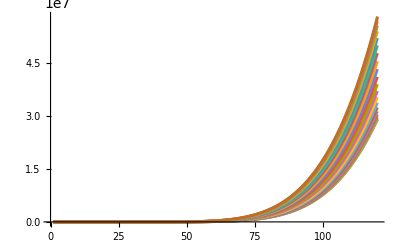

```mathematica
ListLinePlot[plotdata,PlotRange->{All,All}]
```

```mathematica
exportdata=Table[p[[i]][[2;;120]]*197.33^3,{i,1,21}];
```

```mathematica
Table[Export["V"<>ToString[i]<>".dat",p[[i]][[1;;120]]*197.33^3],{i,1,21}]
```

{V1.dat,V2.dat,V3.dat,V4.dat,V5.dat,V6.dat,V7.dat,V8.dat,V9.dat,V10.dat,V11.dat,V12.dat,V13.dat,V14.dat,V15.dat,V16.dat,V17.dat,V18.dat,V19.dat,V20.dat,V21.dat}

```mathematica
Export["T.dat",T]
```

T.dat